### Функции

```mathematica
ReadSnapHeader[fname_String]:=Block[{ReadTilleq,fin,t,count,np,KolProc,n1,n2,n3,Rey,a,},
ReadTilleq[stream_,type_,opts1___]:=Block[{},
		Skip[stream,Record,RecordSeparators->{"="}];Skip[stream,Character];Return[Read[stream,type,opts1]];
		];
	fin=OpenRead[fname,BinaryFormat->True];
	t = ReadTilleq[fin, Real];
	count = ReadTilleq[fin, Number];
	np = ToExpression[ReadTilleq[fin, Record, RecordSeparators->{"\n"}]];
	KolProc = Times@@np;
	n1 = ReadTilleq[fin, Number];
	n2 = ReadTilleq[fin, Number];
	If[!$2d,n3 = ReadTilleq[fin, Number]];
	Rey = ReadTilleq[fin, Real];
Close[fin];
{t,count,np,{n1,n2,n3},Rey}
	]
```

```mathematica
ReadZipSnapHeader[fname_String]:=Block[{temp,out},
name=StringReplace[fname,".zip"->""](*<>".snp"*);
temp=First[Import[fname,{"*.snp","Binary"}]];
Export[name,temp,"Binary","DataFormat"-> "Byte"];
out=ReadSnapHeader[name];
(*Close[name];*)
DeleteFile[name];
Return[out]
]
```

```mathematica
ScanSnaps:=Block[{files},
If[$ZIP===True,files=FileNames["*.snp.zip"],files=FileNames["*.snp"]];
If[Length[files]==0,Print["Файлов не найдено"];Return[{}]];
If[$ZIP===True,
info=ReadZipSnapHeader/@files,
info=ReadSnapHeader/@files];
If[Length[Union[info⟦All,4⟧]]==1,
Print["Сетка одинаковая: ",info⟦1,4⟧];
If[Length[Union[info[[All,3]]]]==1,
Print["Деление на процессы одинаковое: ",info⟦1,3⟧];
Print["Структура у всех одинаковая"];Return[info⟦All,{1,2,5}⟧],
Print["\tДля деления ",#," есть снимки:\n",info⟦First/@Position[info,#],{1,2,5}⟧]&/@Union[info[[All,3]]];],
Map[Function[mesh,
If[Length[Union[info[[First/@Position[info,mesh],3]]]]==1,
Print["Для сетки ",mesh," деление на процессы одинаковое: ",info⟦Position[info,mesh]⟦1,1⟧,3⟧, " и есть снимки:\n",info⟦First/@Position[info,mesh],{1,2,5}⟧],
Print["Для сетки ",mesh," есть несколько делений на процессы:"];
Print["\tДля деления ",#," есть снимки:\n",info⟦Intersection[First/@Position[info,mesh],First/@Position[info,#]],{1,2,5}⟧]&/@Union[info[[All,3]]]
]
],Union[info[[All,4]]]
];
];
Transpose[info]
]
```

### Процесс

```mathematica
ReadZipSnapHeader["screw_64_1020.snp.zip"]
```

```mathematica
ReadSnapHeader["screw_2_187.snp"]
```

```mathematica
$ZIP=False;
```

```mathematica
$2d=True;
```

```mathematica
infos=ScanSnaps
```

```mathematica
infos=SortBy[ScanSnaps,#⟦2⟧&]
```

Сетка одинаковая: {100,100,n3}

Деление на процессы одинаковое: {4,4}

Структура у всех одинаковая

{{4.00102,4138,10.},{8.00115,5962,20.},{12.0012,7169,30.},{16.0038,8078,40.},{20.0037,8803,50.},{24.0028,9410,60.},{28.0051,9929,70.},{32.0082,10383,80.},{36.0021,10785,90.},{40.0052,11150,100.},{44.0072,11481,110.},{48.0083,11786,120.},{52.0107,12067,130.},{56.0008,12326,140.},{60.0119,12569,150.},{64.0159,12796,160.},{68.0105,13011,170.},{72.0088,13212,180.},{76.0169,13404,190.},{80.015,13587,200.}}

```mathematica
Union[Last/@infos]
```

{10.,20.,30.,40.,50.,60.,70.,80.,90.,100.,110.,120.,130.,140.,150.,160.,170.,180.,190.,200.}

```mathematica
Position[infos,{_,_,#},1]⟦-1⟧&/@Union[Last/@infos]
```

{{4},{8},{12},{16},{20},{24},{28},{32},{36},{40}}

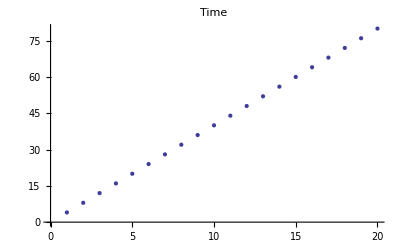
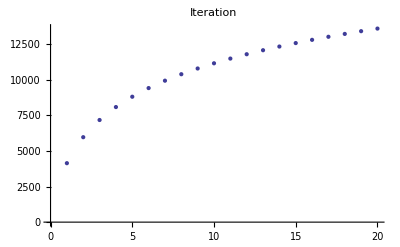
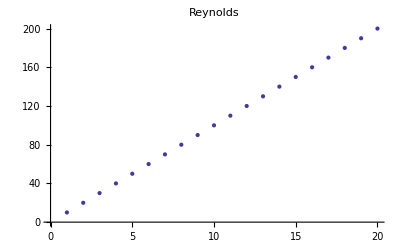

```mathematica
MapThread[ListPlot[#1,PlotLabel->#2]&,{CutList[Union[infos]ᵀ,100],{"Time","Iteration","Reynolds"}}]
```

```mathematica
dellist=Complement[infos[[All,2]],#⟦2⟧&/@Extract[infos,Position[infos,{_,_,#},1]⟦-1⟧&/@Union[Last/@infos]]]
```

{1315,2295,3204,4596,5057,5508,6264,6566,6867,7397,7624,7850,8260,8441,8622,8956,9108,9259,9542,9671,9799,10043,10156,10271,10484,10585,10685,10877,10969,11059,11234,11316,11399,11559,11634,11710,11857,11927,11996,12133,12197,12262,12389,12448,12509,12627,12683,12739,12850,12903,12957,13062,13112,13162,13260,13308,13356,13450,13496,13541}

```mathematica
dellist=Complement[infos[[All,2]],CutList[infos[[All,2]],100]]
```

```mathematica
DeleteFile["pumpflow_16_"<>PadLeft[Characters@ToString[#],4,"0"]<>".snp"]&/@dellist;
```

```mathematica
Block[{prefix1="pumpflow_16_",prefix2},
prefix2="pumpflow";
RenameFile[prefix1<>ToString[#⟦2⟧]<>".snp",prefix2<>"("<>ToString[Floor[#⟦3⟧]]<>").snp"]]&/@infos
```